```mathematica
$Assumptions = {t,μ,λ}∈Reals&&t>0&&μ>0&&λ>0
```

(t|μ|λ)∈ℝ&&t>0&&μ>0&&λ>0

```mathematica
PDF[InverseGaussianDistribution[μ,λ],t]
```

Piecewise[{{(ⅇ^(-(λ (t-μ)^2)/(2 t μ^2)) √(λ/t^3))/(√(2 π)), t>0}, {0, True}}]

```mathematica
Plot[PDF[InverseGaussianDistribution[μ,λ],t],{t,0,30}]
```

-Graphics-

```mathematica
CDF[InverseGaussianDistribution[μ,λ],t]
```

Piecewise[{{1/2 Erfc[(√(λ/t) (-t+μ))/(√2 μ)]+1/2 ⅇ^((2 λ)/μ) Erfc[(√(λ/t) (t+μ))/(√2 μ)], t>0}, {0, True}}]

```mathematica
Plot[CDF[InverseGaussianDistribution[μ,λ],t],{t,0,30}]
```

-Graphics-

```mathematica
tp[t_,μ_,λ_]=PDF[InverseGaussianDistribution[μ,λ],t]/(1-CDF[InverseGaussianDistribution[μ,λ],t])
```

Piecewise[{{(ⅇ^(-(λ (t-μ)^2)/(2 t μ^2)) √(λ/t^3))/(√(2 π)), t>0}, {0, True}}]/(1-(Piecewise[{{1/2 Erfc[(√(λ/t) (-t+μ))/(√2 μ)]+1/2 ⅇ^((2 λ)/μ) Erfc[(√(λ/t) (t+μ))/(√2 μ)], t>0}, {0, True}}]))

```mathematica
tp[t_,μ_,λ_] = FullSimplify[tp[t,μ,λ]]
```

-(ⅇ^(-(λ (t-μ)^2)/(2 t μ^2)) √(2/π) √(λ/t^3))/(-2+Erfc[(√(λ/t) (-t+μ))/(√2 μ)]+ⅇ^((2 λ)/μ) Erfc[(√(λ/t) (t+μ))/(√2 μ)])

```mathematica
μ=0.08
λ=0.02
```

0.08

0.02

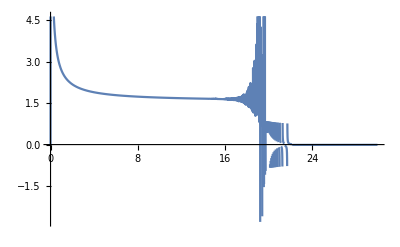

```mathematica
Plot[tp[t,μ,λ],{t,0,30}]
```